```mathematica
dat = Import["/Users/daria/OpticalAbsorptionTBG/monolayer_energies_20_0.005_lined.txt","Data"];
dat⟦1⟧⟦1⟧
```

-0.361209994972224946

```mathematica
dat⟦1000⟧⟦2⟧
```

0.0817723905054544148

Part::partd: Part specification List⟦2⟧ is longer than depth of object.

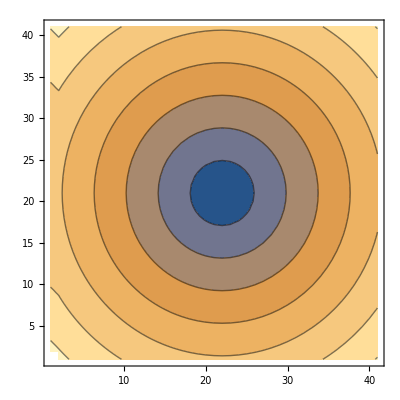

```mathematica
table = Table[dat⟦(i+Num)*(2*Num+1)+(j+Num)⟧⟦2⟧,{i,-Num,Num,1},{j,-Num,Num,1}];
ListContourPlot[table]
```